Quick Quantum Computing with Q3 |

Quantum States in Q3paclet:Q3/tutorial/QuickQuantumComputingWithQ3#2114153471 | Measurements in Q3paclet:Q3/tutorial/QuickQuantumComputingWithQ3#616516018
Operators on Qubits in Q3paclet:Q3/tutorial/QuickQuantumComputingWithQ3#1564669078 | Quantum Circuit Modelpaclet:Q3/tutorial/QuickQuantumComputingWithQ3#2021838213

Q3 provides many utilities and mechanism to facilitate the study of quantum computation and information. In this document, we explain some basic usages of Q3 in the context of quantum computation and quantum information are explained.

For more advanced applications of Q3, see the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

Qubitpaclet:Q3/ref/QubitQ3 Package Symbol | A speciespaclet:Q3/ref/speciesQ3 Package Symbol representing a quantum bit or qubit for short.
Ketpaclet:Q3/ref/KetQ3 Package Symbol | Represents a quantum state of a system of speciespaclet:Q3/ref/speciesQ3 Package Symbol.
Basispaclet:Q3/ref/BasisQ3 Package Symbol | Generates the basis of the Hilbert space associated with a system of speciespaclet:Q3/ref/speciesQ3 Package Symbol.
Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol | Gives the matrix representation of operators on the Hilbert space associated with a system of speciespaclet:Q3/ref/speciesQ3 Package Symbol.
ExpressionForpaclet:Q3/ref/ExpressionForQ3 Package Symbol | Recovers an operator expression from a matrix representation.
Elaboratepaclet:Q3/ref/ElaborateQ3 Package Symbol | Transforms an expression to a more explicit form.
Measurementpaclet:QuantumPlaybook/ref/MeasurementQuantumPlaybook Package Symbol | Represents a measurement of Pauli operators (including tensor products of single-qubit Pauli operators)
MeasurementOddspaclet:QuantumPlaybook/ref/MeasurementOddsQuantumPlaybook Package Symbol | Analyses the probabilities and post-measurement states of a Pauli measurement on a quantum state.

Q3 functions useful in quantum computation and quantum information.

Make sure that the Q3 package is loaded to use the demonstrations in this document.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Quantum States in Q3

A quantum bit, or qubit for short, is a quantum two-level system. It is the elementary unit of quantum computers. Each qubit is associated with a two-dimensional Hilbert space (≃ ℂ^2). The computational basis of the Hilbert space is denoted by {0,1}.

The Hilbert space associated with a system of n qubits is constructed with the tensor product of the Hilbert spaces of individual qubits and is isomorphic to ℂ^2⊗ℂ^2⊗⋯⊗ℂ^2=(ℂ^2)^(⊗n). The standard tensor-product basis of the Hilbert space is given by

{s_1⊗s_2⊗⋯⊗s_n:s_k=0,1}.

Any quantum state ψ in the Hilbert space can be expanded in this basis as

ψ=∑_(s_1=0)^1 ∑_(s_2=0)^1 ⋯∑_(s_n=0)^1 s_1⊗s_2⊗⋯⊗s_n c_(s_1 s_2(⋯s)_n)

for some complex coefficients c_(s_1 s_2(⋯s)_n).

Q3 provides two different ways to represent the computational basis states of an n-qubit system.

Using Ketpaclet:ref/Ket[s_1,s_2,…,s_n] to represent tensor-product state s_1⊗s_2⊗⋯⊗s_n. Although it looks simple, this method becomes quickly tedious as the number of qubits increases. This method is suitable for a small system of qubits.

Using Ketpaclet:ref/Ket[<|Spaclet:Q3/ref/SQ3 Package Symbol[1]→s_1,S[2]→s_2,…,S[n]→s_n|>] represent tensor-product state s_1⊗s_2⊗⋯⊗s_n. It may look complicated at the first glance but is more efficient for a larger system of qubits.

### Method Using Ket[…]

In this method, a computational basis state is represented by Ketpaclet:ref/Ket[s_1,s_2,…].

For example, consider a three-qubit system. Here is the standard tensor-product basis of the system.

```mathematica
bs=Basis[3]
```

{0,0,0,0,0,1,0,1,0,0,1,1,1,0,0,1,0,1,1,1,0,1,1,1}

Each state in the above basis is displayed in the bra-ket notation. Internally, Ketpaclet:ref/Ket[…] is used.

```mathematica
InputForm[bs]
```

{Ket[0, 0, 0], Ket[0, 0, 1], Ket[0, 1, 0], Ket[0, 1, 1], Ket[1, 0, 0], Ket[1, 0, 1], Ket[1, 1, 0], Ket[1, 1, 1]}

A state vector is a linear superposition of the standard basis states.

```mathematica
ket=Ket[0,1,0]-I*Ket[1,0,0]
```

0,1,0-ⅈ 1,0,0

A state vector can be represented by a column vector in the standard tensor-product basis.

```mathematica
vec=Matrix[ket];
vec//MatrixForm
```

(0
0
1
0
-ⅈ
0
0
0)

The original expression in terms of Ketpaclet:ref/Ket[…] may be recovered with ExpressionFor.

```mathematica
new=ExpressionFor[vec]
```

0,1,0-ⅈ 1,0,0

```mathematica
new-ket
```

0

### Method Using Ketpaclet:ref/Ket[<|⋯|>]

In this method, you need to first choose a symbol, say, S, to denote a group of qubits.

```mathematica
Let[Qubit,S]
```

Symbol S declared as qubit can take flavor indices in the form S[j_1,j_2,…,μ]. The preceding flavor indices j_1,j_2,… specifies a particular qubit in the class denoted by the symbol S. The last flavor index μ=0,1,2,3,… refers to the Pauli operator (I,X,Y,Z,…, respectively, to be discussed below) on the qubit specified by the preceding indices j_1,j_2,…. An exceptional case is μ=$paclet:Q3/ref/$Q3 Package Symbol, and S[j_1,j_2,…,$paclet:Q3/ref/$Q3 Package Symbol] refers to the qubit itself (rather than an operator) specified by the indices j_1,j_2,….

Now, a computational basis state is specified by

Ketpaclet:ref/Ket[<|Spaclet:Q3/ref/SQ3 Package Symbol[1,$]→s_1,S[2,$]→s_2,…,S[n,$]→s_n|>].

For example, the logical basis for qubit S[1,$] is comprised of these two states.

```mathematica
v0=Ket[S[1,$]->0]
v1=Ket[S[1,$]->1]
```

␣

1_S_1

They are displayed in the bra-ket notation. Internally, Ketpaclet:ref/Ket[<|⋯|>] is used.

```mathematica
{v0,v1}//InputForm
```

{Ket[<||>], Ket[<|S[1, $] -> 1|>]}

For a two-qubit system, here is the standard tensor-product basis. Recall that different qubits (within the same class referred to by symbol S) are distinguished by the flavor indices.

```mathematica
bs=Basis[S[1],S[2]]
bs//LogicalForm
bs//InputForm
```

{␣,1_S_2,1_S_1,1_S_11_S_2}

{0_S_10_S_2,0_S_11_S_2,1_S_10_S_2,1_S_11_S_2}

{Ket[<||>], Ket[<|S[2, $] -> 1|>], Ket[<|S[1, $] -> 1|>], Ket[<|S[1, $] -> 1, S[2, $] -> 1|>]}

Typing in the special flavor index $ every time you specify a state vector would be cumbersome, and within Ketpaclet:ref/Ket[…], it can be dropped. (Many other functions in Q3 also allow it.)

```mathematica
v0=Ket[S[1]->0]
v1=Ket[S[1]->1]
```

␣

1_S_1

As you can see in the above examples, for the sake of efficiency, qubits in the logical basis state 0 are omitted from Ketpaclet:Q3/ref/KetQ3 Package Symbol[<|…|>]. You can force them to be displayed with LogicalFormpaclet:Q3/ref/LogicalFormQ3 Package Symbol.

```mathematica
ket=v0-I v1
LogicalForm[ket,{S[1,$],S[2,$]}]
LogicalForm[ket,{S[1],S[2]}]
```

␣-ⅈ 1_S_1

0_S_10_S_2-ⅈ 1_S_10_S_2

0_S_10_S_2-ⅈ 1_S_10_S_2

A state vector can be represented by a column vector in the standard tensor-product basis (computational basis). This can be achieved by Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol. For example, consider the following state.

```mathematica
ket=S[1,6]**S[2,6]**Ket[];
ket//LogicalForm
```

1/2 0_S_10_S_2+1/2 0_S_11_S_2+1/2 1_S_10_S_2+1/2 1_S_11_S_2

Get the column-vector representation of it.  Here note that S[{1,2}]={S[1],S[2]} is equivalent to S[{1,2},$paclet:ref/$]={S[1,$paclet:ref/$],S[2,$paclet:ref/$]} inside Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol.

```mathematica
vec=Matrix[ket,S@{1,2}];
vec//MatrixForm
```

(1/2
1/2
1/2
1/2)

Recover the expression in terms of basis states. (Again, $ is automatically attached unless it already exists inside ExpressionForpaclet:Q3/ref/ExpressionForQ3 Package Symbol.)

```mathematica
new=ExpressionFor[vec,S@{1,2}];
new//LogicalForm
```

1/2 0_S_10_S_2+1/2 0_S_11_S_2+1/2 1_S_10_S_2+1/2 1_S_11_S_2

Operators on Qubits in Q3

Any linear operator U on the Hilbert space associated with a system of n qubits can be written as a linear combination of tensor products of single-qubit Pauli operators,

U=∑_(μ_1=0)^4 ∑_(μ_2=0)^4 ⋯∑_(μ_n=0)^4 S^μ_1⊗S^μ_2⊗…⊗S^μ_n c_(μ_1 μ_2... μ_n),

where μ_k=0,1,2,3 with S^0=I, S^1=X, S^2=Y, S^3=Z, and c_(μ_1 μ_2... μ_n) are complex coefficients.

Like state vectors, Q3 provides two different ways to represent the Pauli operators.

Using Paulipaclet:Q3/ref/PauliQ3 Package Symbol[μ_1,μ_2,…,μ_n] to represent tensor product S^μ_1⊗S^μ_2⊗…⊗S^μ_n. This method works consistently with the method using Ketpaclet:ref/Ket[s_1,s_2,…,s_n] for tensor-product basis states. This method is suitable for a small system of qubits.

Using S[j_1,μ_1]**S[j_2,μ_2]**⋯**S[j_n,μ_n](here **  is NonCommutativeMultiplypaclet:ref/NonCommutativeMultiply or Multiplypaclet:Q3/ref/MultiplyQ3 Package Symbol for short) to represent tensor product S^μ_1⊗S^μ_2⊗…⊗S^μ_n. This method works consistently with the method using Ketpaclet:ref/Ket[<|…|>] to represent tensor-product basis state. This method may look complicated at the first glance but is more efficient for a larger system of qubits.

### Method Using Paulipaclet:Q3/ref/PauliQ3 Package Symbol[⋯]

Consider a tensor product of single-qubit Pauli operators.

```mathematica
op=Pauli[1,0,2]
```

X⊗I⊗Y

Consider a state vector.

```mathematica
in=Ket[0,1,0]-Ket[1,0,0]
```

0,1,0-1,0,0

You can act operator op on the above state vector using Multiply or, equivalently, **.

```mathematica
out=op**in
```

-ⅈ 0,0,1+ⅈ 1,1,1

The matrix representation of an operator in the standard tensor-product basis can be obtained using Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol.

```mathematica
mat=Matrix[op];
mat//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | -ⅈ | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ
0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0
ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0)

The operator expression may be recovered with ExpressionFor.

```mathematica
new=ExpressionFor[mat]//Elaborate
```

X⊗I⊗Y

```mathematica
op-new
```

0

For a more advanced demonstration, see Demo: Commutation Relations for Qubits.

### Method Using S[⋯]**S[⋯]**⋯

This is a typical form of a linear operator in this method. Recall that S[j_1,j_2,…,μ] operates on qubit S[j_1,j_2,…,$paclet:ref/$].

```mathematica
op=S[1,1]+I S[1,2]**S[2,2]
```

ⅈ S_1^yS_2^y+S_1^x

```mathematica
op//PauliForm
```

X⊗I+ⅈ Y⊗Y

Consider a state vector.

```mathematica
in=Ket[];
LogicalForm[in,S@{1,2}]
```

0_S_10_S_2

You can act operator op on the above state vector using Multiply (**).

```mathematica
out=op**in;
out//LogicalForm
```

1_S_10_S_2-ⅈ 1_S_11_S_2

Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol converts the operator into a matrix representation in the standard basis of the qubits involved in the expression.

```mathematica
mat=Matrix[op];
mat//MatrixForm
```

(0 | 0 | 1 | -ⅈ
0 | 0 | ⅈ | 1
1 | ⅈ | 0 | 0
-ⅈ | 1 | 0 | 0)

It is a good habit to check the standard basis implied in the matrix representation.

```mathematica
bs=Basis[S[1],S[2]];
bs//LogicalForm
```

{0_S_10_S_2,0_S_11_S_2,1_S_10_S_2,1_S_11_S_2}

You can recover the operator expression from the matrix representation using ExpressionForpaclet:Q3/ref/ExpressionForQ3 Package Symbol.

```mathematica
new=ExpressionFor[mat,S@{1,2}]//Elaborate
op-new
```

ⅈ S_1^yS_2^y+S_1^x

0

MultiplyExppaclet:Q3/ref/MultiplyExpQ3 Package Symbol is another way to generate an operator from other operator.

```mathematica
expr=MultiplyExp[-I S[1,2] ϕ]
Elaborate[expr]
```

ⅇ^(-ⅈ ϕ S_1^y)

Cos[ϕ]-ⅈ S_1^y Sin[ϕ]

Sometimes, it is useful to collectively refer to different Pauli operators on the same qubit. S[j_1,j_2,…,Allpaclet:ref/All] and S[j_1,j_2,…,Fullpaclet:ref/Full] are reserved for this purpose.

```mathematica
S[1,All]
S[2,Full]
```

{S_1^x,S_1^y,S_1^z}

{S_2^0,S_2^x,S_2^y,S_2^z}

Use the above sets to construct some composite expressions. For example, you can construct the Heisenberg Hamiltonian for two spins (qubits).

```mathematica
op=Total[S[1,All]**S[2,All]]
PauliForm[op]
```

S_1^xS_2^x+S_1^yS_2^y+S_1^zS_2^z

X⊗X+Y⊗Y+Z⊗Z

For a more advanced demonstration, see Demo: Commutation Relations for Qubits.

Measurements in Q3

Q3 supports measurement of any Pauli operators (including tensor products of single-qubit Pauli operators).

As a simple example, consider a three-qubit system in the following state.

```mathematica
in=(Ket[]+Ket[S@{1,2,3}->1])/Sqrt[2];
in//LogicalForm
```

(0_S_10_S_20_S_3+1_S_11_S_21_S_3)/(√2)

Suppose that you want to measure the Pauli Z operator (i.e., S[1,3]) on qubit S[1,$]. From the above state, we expect two measurement outcomes 0 and 1 (corresponding to eigenvalues ±1 of S[1,3]) and corresponding post-measurement states with equal probability.

```mathematica
MeasurementOdds[in,S[1,3]]//Garner//LogicalForm
```

<|0→{1/2,0_S_10_S_20_S_3},1→{1/2,1_S_11_S_21_S_3}|>

Performing the measurement, you can get random outcomes according to the probabilities shown above.

```mathematica
out=Measurement[S[1,3]][in];
LogicalForm[out,S@{1,2,3}]
```

1_S_11_S_21_S_3

```mathematica
msr=Measurement[S[1,3]];
Table[msr[in],10]//LogicalForm
```

{0_S_10_S_20_S_3,0_S_10_S_20_S_3,0_S_10_S_20_S_3,1_S_11_S_21_S_3,1_S_11_S_21_S_3,1_S_11_S_21_S_3,0_S_10_S_20_S_3,0_S_10_S_20_S_3,0_S_10_S_20_S_3,1_S_11_S_21_S_3}

```mathematica
Table[msr[in];Readout[S[1,3]],10]
```

{1,0,0,1,1,1,1,1,0,1}

Collecting the random outcomes, you can infer the probability distribution.

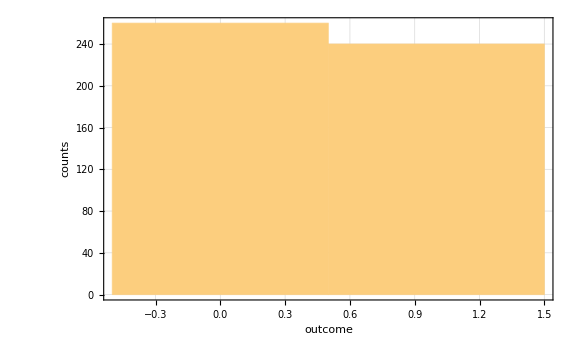

```mathematica
data=Table[msr[in];Readout[S[1,3]],500];
Histogram[data,FrameLabel->{"outcome","counts"}]
```

As another example, let us now consider a collective measurement, say, the measurement of Z⊗Z. Suppose that a system of two qubits in the following state.

```mathematica
in=Basis[S@{1,2}].{1,1,I,-I};
in//LogicalForm
```

0_S_10_S_2+0_S_11_S_2+ⅈ 1_S_10_S_2-ⅈ 1_S_11_S_2

Analyse the possible measurement outcomes, the corresponding probabilities and post-measurement states. Here note that outcomes 0 and 1 refer to eigenvalues ±1 of Z⊗Z, respectively. (Recall that any Pauli operator only has eigenvalues ±1.) It is also important to note that the post-measurement states maintains the phase coherence inherited from the input state.

```mathematica
MeasurementOdds[in,S[1,3]**S[2,3]]//Map[Simplify]//LogicalForm
```

<|0→{1/2,(0_S_10_S_2-ⅈ 1_S_11_S_2)/(√2)},1→{1/2,(0_S_11_S_2+ⅈ 1_S_10_S_2)/(√2)}|>

As in the above example, one can infer the probability distribution by sampling the outcomes.

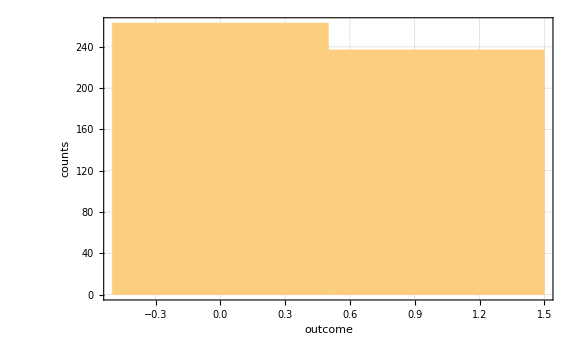

```mathematica
data=Table[Measurement[S[1,3]**S[2,3]][in];Readout[S[1,3]**S[2,3]],500];
Histogram[data,FrameLabel->{"outcome","counts"}]
```

Quantum Circuit Model

Q3 fully supports the quantum circuit model of quantum computation through QuantumCircuitpaclet:Q3/ref/QuantumCircuitQ3 Package Symbol.

S[j_1,j_2,…,1|2|3] | The Pauli X, Y, and Z, respectively, on qubit S[j_1,j_2,…,$].
S[j_1,j_2,…,6] | The Hadamard gate on qubit S[j_1,j_2,…,$].
S[j_1,j_2,…,7] | The quadrant phase gate on qubit S[j_1,j_2,…,$].
S[j_1,j_2,…,8] | The octant phase gate on qubit S[j_1,j_2,…,$].
Rotationpaclet:Q3/ref/RotationQ3 Package Symbol | Single-qubit rotation gate.
Phasepaclet:Q3/ref/PhaseQ3 Package Symbol | Single-qubit (relative) phase shift.
CNOTpaclet:Q3/ref/CNOTQ3 Package Symbol | The CNOT gate.
Toffolipaclet:Q3/ref/ToffoliQ3 Package Symbol | The Toffoli gate.
Fredkinpaclet:Q3/ref/FredkinQ3 Package Symbol | The Fredkin gate.
ControlledUpaclet:Q3/ref/ControlledUQ3 Package Symbol | Controlled-unitary gate.
Oraclepaclet:Q3/ref/OracleQ3 Package Symbol | Quantum oracle.

Some frequently used quantum circuit elements in the quantum circuit model of quantum computation.

Here is an simple example of quantum circuit.

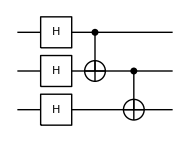

```mathematica
qc=QuantumCircuit[S[{1,2,3},6],CNOT[S[1],S[2]],CNOT[S[2],S[3]]]
```

One can convert a quantum circuit to an analytic expression.

```mathematica
op=ExpressionFor[qc]
```

-Graphics-

One can also directly apply a quantum circuit to an input state.

```mathematica
in=Ket[];
LogicalForm[in,S@{1,2,3}]
```

0_S_10_S_20_S_3

```mathematica
out=qc**in;
out//LogicalForm
```

(0_S_10_S_20_S_3)/(2 √2)+(0_S_10_S_21_S_3)/(2 √2)+(0_S_11_S_20_S_3)/(2 √2)+(0_S_11_S_21_S_3)/(2 √2)+(1_S_10_S_20_S_3)/(2 √2)+(1_S_10_S_21_S_3)/(2 √2)+(1_S_11_S_20_S_3)/(2 √2)+(1_S_11_S_21_S_3)/(2 √2)

The above output state should be the same as the result from acting operator expression op.

```mathematica
new=op**in;
new//LogicalForm
```

(0_S_10_S_20_S_3)/(2 √2)+(0_S_10_S_21_S_3)/(2 √2)+(0_S_11_S_20_S_3)/(2 √2)+(0_S_11_S_21_S_3)/(2 √2)+(1_S_10_S_20_S_3)/(2 √2)+(1_S_10_S_21_S_3)/(2 √2)+(1_S_11_S_20_S_3)/(2 √2)+(1_S_11_S_21_S_3)/(2 √2)

```mathematica
out-new
```

0

It is possible to multiply the quantum circuit with an operator as well.

```mathematica
qc**S[1,1]
op**S[1,1]
```

-Graphics-

-Graphics-

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪The Postulates of Quantum Mechanics
▪Quantum Computation: Overview
▪Quantum Algorithms
▪Quantum Noise and Decoherence
▪Quantum Error-Correction Codes
▪Quantum Information Theory
▪Demo: Commutation Relations for Qubits

| Related Links
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).
An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/
The Wolfram Language: Fast Introduction for Programmershttp://www.wolfram.com/language/fast-introduction-for-programmers/